```mathematica
kTq = 25 10^-3
```

1/40

```mathematica
Idiode[Vbe_] :=10^-12 ( Exp[Vbe/kTq]-1)
```

```mathematica
Idiode[5]
```

(-1+ⅇ^200)/1000000000000

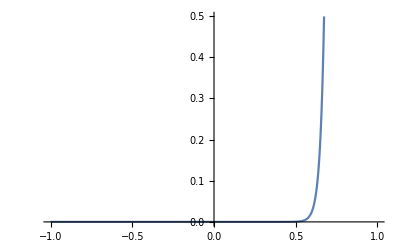

```mathematica
diodeiv = Plot[Idiode[x],{x,-1,1}]
```

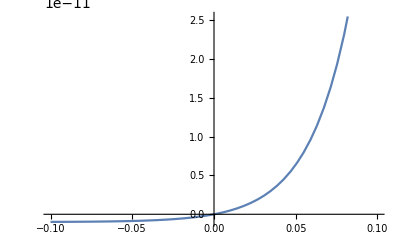

```mathematica
diodeivzoom=Plot[Idiode[x],{x,-.1,.1}]
```

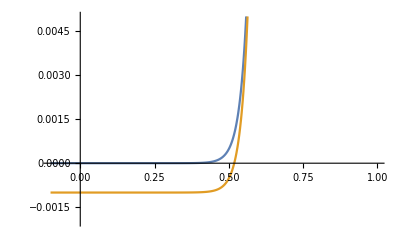

```mathematica
solarcell2 = Plot[{Idiode[x],-10^-3 + Idiode[x]},{x,-.1,1},PlotRange->{{-.1,1},{-.002,.005}}]
```

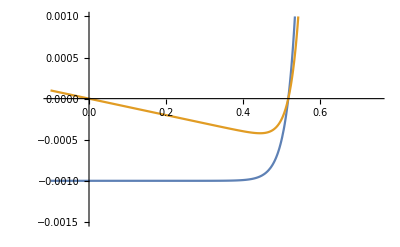

```mathematica
solarcell = Plot[{-10^-3 + Idiode[x],x*(-10^-3 + Idiode[x])},{x,-.1,.75},PlotRange->{{-.1,.75},{-.0015,.001}}]
```

```mathematica
SetDirectory["~/Desktop"]
```

/Users/niknejad/Desktop

```mathematica
Export["solarcell2.pdf",solarcell2]
```

solarcell2.pdf

```mathematica
Export["diodeiv.pdf",diodeiv]
```

diodeiv.pdf

```mathematica
Export["diodeiv_zoom.pdf",diodeivzoom]
```

diodeiv_zoom.pdf

```mathematica
Export["solarcell.pdf",solarcell]
```

solarcell.pdf

```mathematica
?Plot
```

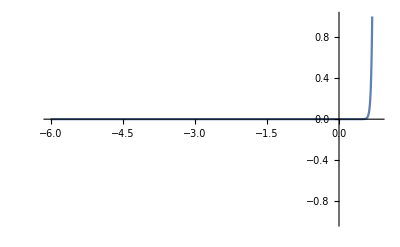

```mathematica
diodeiv2 = Plot[Idiode[x],{x,-6,1},PlotRange->{{-6,.8},{-1,1}}]
```